{{Version V1.1,Start Time: 14-03-2022_181207},{Time,Angle (deg)},{225.886,-0.395589},{225.888,-0.391256},970427,{2314.46,-0.500585},{2314.46,-0.525372},{2314.46,-0.52032},{2314.46,-0.519864}}
 |  |  |  |

Plot unsmoothed points

separate elements

Recombine original truncated data Elements

Plot original elements

Process Bilateral Smoothing

Recombine BiLateral Elements

Perform Second BiLateral Smoothing of Original BiLateral Table

Recombine Bilateral Elements

Perform Third BiLateral Smoothing of Second BiLateral Table

Perform Moving Median Smoothing of third BiLateral list

Recombine Moving Median Elements

{960434}

Separate time and angle from data set

Find Peaks

Peaks = {{1,-0.439043},{145714,0.325175},{751911/2,0.212844},{603042,0.0734151},{1724001/2,0.0490199},{970433,970435}}

Number of peaks = 6

Recombine peaks and associated time

Compute wave properties

{6}

{{225.886,-0.439043},{560.095,0.325175},{1052.69,0.212844},{1534.56,0.0734151},{2084.41,0.0490199},{970434,970435}}

{{808.528,-0.525659},{1293.66,-0.557788},{1809.22,-0.544751},{2199.46,-0.380911}}

-Graphics-

referenceAxis = -0.100242

amplitude = -0.425417

period = 492.594

dampingCoefficient = 0.112331

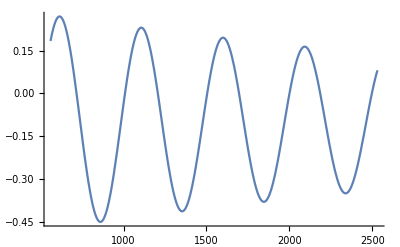

```mathematica
(*runData = Import["/Users/plentz/Documents/Parallax621Project/experiment/Results/2e/run1/Oscillation_NoLaserMass_Centered_22Mar22_8p.csv", "CSV"]*)
runData = Import["/Users/plentz/Documents/Parallax621Project/experiment/Results/2d/run2/Oscillation_JustRotated_14MAR22_6PM.csv", "CSV"]
smoothZoeDataSet[runData]
generateSineWaveListFromZOEOscillationDataSet[timeAngleDataSet]
peaksAndTime
troughsAndTime
ListLinePlot[{timeAngleDataSet, peaksAndTime, troughsAndTime},PlotRange->{{0,4500},{1.3,-1.3}}]
Print["referenceAxis = ", referenceAxis]
Print["amplitude = ", amplitude]
Print["period = ", period]
Print["dampingCoefficient = ", dampingCoefficient = dampingCoefficient1 (*(dampingCoefficient1 + dampingCoefficient2)/2*)]
Plot[referenceAxis - E^((-dampingCoefficient/period) t)Abs[amplitude]Cos[2 Pi t/(period) + Pi/2],{t, startTime,startTime+4 period},PlotRange->{{0,4500},{1.3,-1.3}}]
```